```mathematica
(* processing selection sort times *)
data = Import["/Users/john/structures/assignment2/merge.csv", "CSV"];
wordCounts = data[[All, 1]];
comparisons = data[[All, 2]];
swaps = data[[All, 3]];
times = data[[All, 4]];
```

8728.08-0.840075 words+0.0000199497 words^2

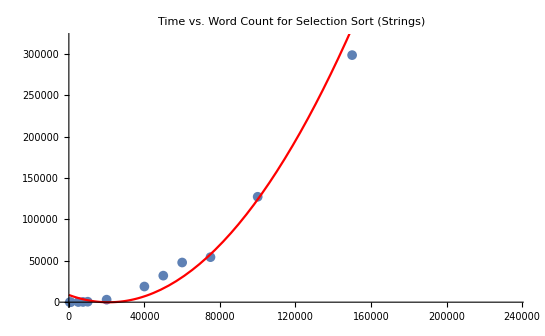

Set::write: Tag List in {499500, 49995000, 704982704, 1634976888, 199990000, 2051180779, 799980000, 124750, 12497500, 1249975000, 1799970000, 28121250, 1482504796}[words_] is Protected.

2.35215×10^8+9215.97 words

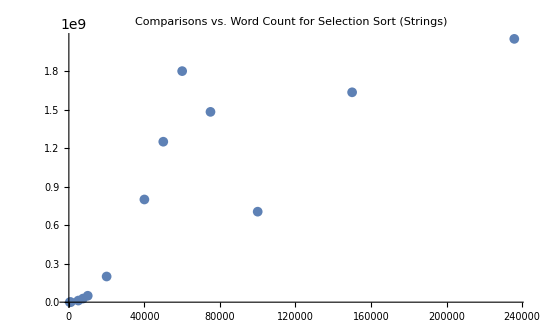

```mathematica
time[words_] = Fit[Transpose[{wordCounts, times}], {1, words, words^2}, words]

Show[ListPlot[Transpose[{wordCounts, times}]], Plot[time[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Time vs. Word Count for Merge Sort (Strings)"]

comparisons[words_] = Fit[Transpose[{wordCounts, comparisons}], {1, words}, words]

Show[ListPlot[Transpose[{wordCounts, comparisons}]], Plot[comparisons[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Comparisons vs. Word Count for Merge Sort (Strings)"]
```